```mathematica
$Path=Prepend[$Path,"G:\\HOME\\anton\\roundabout"];
```

```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["Run"]
```

D:\programs\icmm\tor2DKolm\Run

```mathematica
SetDirectory["d:\\home\\anton\\programs\\tor2d\\tor\\Debug"]
```

d:\home\anton\programs\tor2d\tor\Debug

```mathematica
SetWorkDir["2017-10-02\\Re6000"]
```

D:\programs\icmm\tor2DKolm\2017-10-02\Re6000

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
UnsortedUnion[x_,ndig_:4]:=N[Reap[Sow[1,Round[10^ndig x]],_,#1&]⟦2⟧10^-ndig];
```

### Разбор логов

```mathematica
text=Import["message1.dat","Text"];
```

```mathematica
StrMsg[msg_String]:="(?s)(message of proc#(\\d+) at )?t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>msg
StrChg[par_String]:=StrMsg[par<>" was changed to"]
```

```mathematica
StrChg[par_String]:="t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>par<>" was changed to";
```

```mathematica
Ret=StringCases[text,RegularExpression[StrChg["Re"]]:>ToExpression["$3"]]
```

```mathematica
StringCases[text,RegularExpression[StrMsg["(.*?)"]]:>"$0"]//Length
```

```mathematica
StringCases[text,RegularExpression[StrChg["rc"]]:>"$3"]
```

```mathematica
cs=StringCases[text,RegularExpression[StringJoin["(?s)(",StrChg["rc"],")?(.+?)(?=(",StrChg["rc"],")|$)"]]:>"$0"];cs={StringCases[#,RegularExpression[StrChg["rc"]]->"$3"],StringCases[#,RegularExpression[StrChg["Re"]]->"$3"],StringCases[#,RegularExpression[StrChg["omega"]]->"$3"],StringCases[#,RegularExpression[StrMsg["snap is done"]]->"$5"]}&/@cs;
TableForm[{#⟦1⟧,#⟦2⟧,#[[3]],{#⟦4⟧}}&/@cs]
```

```mathematica
cs[[1,1]]={"0.5"};cs[[1,2]]={"1.00000"};
```

```mathematica
cs[[1,1]]={"0.0"};
```

```mathematica
cs=Most[cs]
```

```mathematica
ListPlot[ToExpression/@cs[[2,2]]]
```

```mathematica
fins={ToExpression@#[[1,1]],ToExpression@Last[#[[2]]],ToExpression@Last[#[[3]]],ToExpression@Last[#[[4]]]}&/@Select[cs,Last[#]≠{}&]
```

{{0.5,1.,-0.6,130174},{0.5,1.,-0.5,134662},{0.5,1.,-0.4,227942},{0.5,1.,-0.3,166877},{0.5,1.,-0.2,149164},{0.5,1.,-0.1,144389},{0.95,0.725,-0.2,147408},{0.95,0.725,-0.3,157889},{0.95,0.725,-0.4,161295},{0.95,0.725,-0.5,169961},{0.95,0.725,-0.6,161321},{0.95,0.725,-0.7,152387},{0.95,0.725,-0.1,144389},{0.01,7.,-0.1,106204},{0.01,7.,-0.2,106407},{0.01,7.,-0.3,106614},{0.01,7.,-0.4,106860},{0.01,7.,-0.5,106986},{0.01,7.,-0.6,107317},{0.01,7.,-0.7,107673},{0.5,10.,-0.01,165868},{0.5,10.,-0.015,164913},{0.5,10.,-0.02,169399},{0.5,10.,-0.025,168443},{0.5,10.,-0.03,165305},{0.5,10.,-0.035,171249}}

```mathematica
fins=StringCases[text,RegularExpression["t=(\\d*100(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=(\\d+(\\.\\d+)?) sec:\nsnap is done"]:>{"$1","$3","$4"}]
```

```mathematica
StringReplace[StringDrop["="<>StringJoin[#<>"+"&/@Transpose[fins][[2]]],-1],"."->","]
```

```mathematica
ListPlot[Ret,PlotRange->{10,All},PlotLabel->Last[Ret],Joined->True]
Last[Ret]
```

## Общие тенденции

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{2517,2.60616}

```mathematica
Scan[Print[PrintRange[#,{0,0.007}]]&,CutList[WithoutFict[#[[2]],3]&/@lv,20]]
```

```mathematica
ListPlot[{First[#],Max[WithoutFict@Last[#]]}&/@lv]
```

```mathematica
Export["energy0.dat",Transpose@Join[{ltm},len⟦All,2⟧,Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz},{2}]]]
```

```mathematica
Export["energy0.dat",Transpose[len]]
```

energy0.dat

```mathematica
Dimensions/@{ltm,len,mp}
```

{{78394},{14,78394},{78394,2}}

```mathematica
FileNames["en*"]
```

{}

Import["en.zip", "energy.dat", "Elements" -> "Table"]
Import["energy.dat", "Table"]

```mathematica
len=Transpose[Fold[If[#2⟦1⟧>#1⟦-1,1⟧,Append[#1,#2],#1]&,{First[Transpose[len]]},Transpose[len]]];
```

```mathematica
Dynamic[Refresh[{
len=Transpose[Select[Import["energy.dat","Table"],0<First[#]&]];
ltm=First[len];
PrintRange[dif[Union[ltm]],All,PlotLabel->{20Length[ltm],Last[ltm]}],
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),All,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]}
,UpdateInterval->5]]
```

```mathematica
len1=Import["energy(kappa=0.30,Re=6000).dat","Table"];Length[len1]
```

118901

```mathematica
len1=Import["energy.dat","Table"];Length[len1]
```

13932

Get::noopen: Cannot open Graphics`Graphics`.

Needs::nocont: Context Graphics`Graphics` was not created when Needs was evaluated.

Set::write: Tag ListLinePlot in SyntaxInformation[ListLinePlot] is Protected.

Get::noopen: Cannot open Graphics`ContourPlot3D`.

Needs::nocont: Context Graphics`ContourPlot3D` was not created when Needs was evaluated.

Get::noopen: Cannot open Utilities`FilterOptions`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context Utilities`FilterOptions` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

Part::partd: Part specification Global`bounds⟦1⟧ is longer than depth of object.

Part::partd: Part specification Global`bounds⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListNumerics::lackinfo: You should define <coord> and <bounds> before using functions of this package

Global`Text::shdw: Symbol Text appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

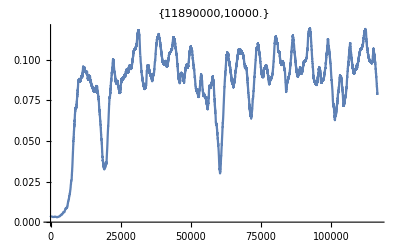

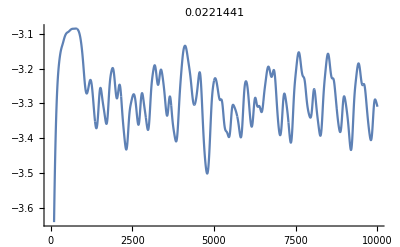

```mathematica
len=Transpose[Select[len1,0<First[#]&]];
ltm=First[len];PrintRange[Smooth@dif[Union[ltm]],All,PlotLabel->{100Length[ltm],Last[ltm]}]
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),Automatic,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]
```

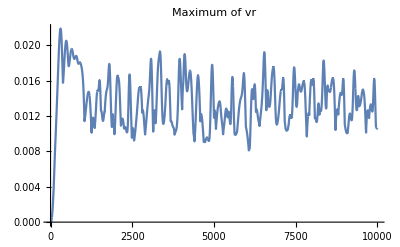
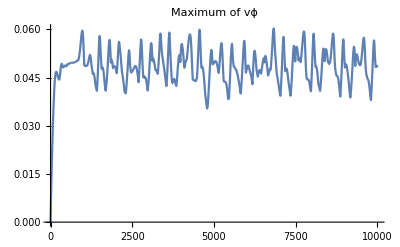
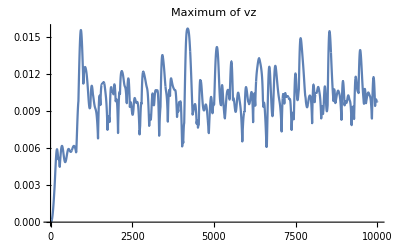
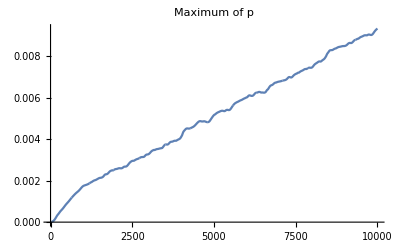

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,10^Log[10,#⟦2⟧]}&,{mvx,mvy,mvz,mp},{2}],{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of p"}}]
```

```mathematica
Smooth[l_,part_:0.02]:=MovingAverage[l,⌈part Length[l]⌉]
```

```mathematica
ListLogPlot[dif@Smooth@mvy]
```

```mathematica
ListLimit[Take[mvy,-Min[⌊(Length[mvy]-First[Ordering[Last/@(dif@Smooth@mvy),50]])/3⌋,Length[mvy]]]//Smooth,CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError,LimitPlot,PolynomDegree}]
```

```mathematica
ListPlot[{1/(First[#]-685),Last[#]}&/@Take[mvy,-1000],PlotRange->{{0,Automatic},All}]
```

```mathematica
ListPlot[Take[mvy,-2000]//Smooth]
```

```mathematica
{maxvx,maxvy,maxvz,mqvx,mqvy,mqvz}=ListLimit[Take[Smooth[#],-Min[500,Length[mvy]-5]],CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError}]&/@{mvx,mvy,mvz,qvx,qvy,qvz}
```

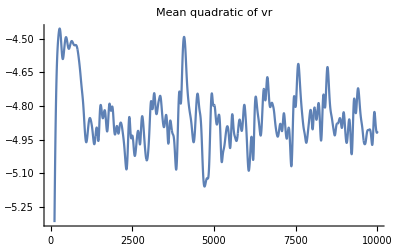
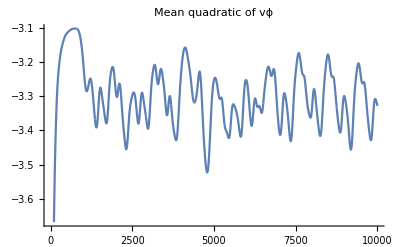
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{qvx,qvy,qvz,qp},{2}],{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{mdvx,mdvy,mdvz,mdp},{2}],{"Max difference of vr","Max difference vϕ","Max difference of vz","Max difference of p"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Обработка массивов

## Начало

```mathematica
dump=Release[ReadList["pumpflow0.dmp",Hold[Expression]]/.{a_+E*b_->b*10^a}];
{coor,bounds}=ReadAuxFiles2D[{"coord"},ShiftVector->{0,0},ProcDistrib->{2,2},NumberOfRefs->2];
```

```mathematica
Max/@Drop[dump,6]
```

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
ReadDrawSection["pumpflow(0.5).snp",Text2D,5]
```

```mathematica
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{1,1},NumberOfRefs->2];
Print[bounds];
```

{{-1.1875,1.1875},{-1.1875,1.1875}}

```mathematica
ACPackages`ACTextSnapManipulation`Private`ghost=6;
```

```mathematica
FileNames["*.snp"]
```

{sinflow_256_1993593.snp,sinflow_256_2008272.snp}

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFiles2D["pumpflow",".dmp",5,PrintInfo->None];
```

```mathematica
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{16,16},NumberOfRefs->2];
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["sinflow_256_2008272.snp",5,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{16,16},NumberOfRefs->2];
Print[bounds];
```

{16,16}

{1000.,2008272,512,512,4500.}

ghost=6

{{-1.,1.},{-1.,1.}}

```mathematica
{#⟦2⟧,Last[#]}&@Union[Flatten[p]]
```

{-110.47,0}

```mathematica
Max/@{p,vx,vy,vz,nut}
```

{0.0019188,0.01263,0.062988,0.014966,0.00022222}

```mathematica
Max[vy]4500
```

283.446

```mathematica
asim[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
√(Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)]/Mean[Flatten@(arr^2)])
]
```

```mathematica
asim1[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
√Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)]
]
```

```mathematica
asim2[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
1/Max[Abs[arr]](√Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)])
]
```

```mathematica
{asim[#⟦2⟧],asim[#⟦3⟧],asim[#⟦4⟧,-1]}&/@{p,vx,vy,vz,nut}
```

```mathematica
Show2x[ListPlot3D[Transpose[#],PlotRange->All,DisplayFunction->Identity]&,{p,vx,vy,nut}]
```

```mathematica
Union[Flatten[nut]]
```

```mathematica
ListPlot3D[WithoutFict@Transpose[nut],PlotRange->All]
```

```mathematica
Manipulate[PrintRange[Transpose[{coor⟦1⟧,ND[vy[[All,⌊Length[Transpose[vy]]/2⌋]],order,0.02,d]}],All,PlotLabel->Length[ND[vy[[All,⌊Length[Transpose[vy]]/2⌋]],order,0.02,d]]],{order,1,5,1},{d,0,4,1}]
```

```mathematica
PrintRange[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]]
```

```mathematica
PrintRange[dif@Transpose[WithoutFict/@{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]]
```

```mathematica
shift=Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
```

```mathematica
With[{arr=vz},{Mean[Flatten@(Table[arr⟦All,i⟧+arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)],Mean[Flatten@(arr^2)]}]
```

{7.34918×10^-9,3.16576×10^-9}

```mathematica
With[{arr=vz},ListContourPlot/@{arr,Table[arr⟦All,i⟧+arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]}]
```

```mathematica
ListContourPlot[GetInner[Transpose[vy]],PlotRange->All,Contours->40]
```

```mathematica
Export["vRe=4500kappa=0.3.png",%,ImageResolution->400,ImageSize->500];
```

```mathematica
ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine]
```

```mathematica
Export["wRe=4500kappa=0.3.png",%,ImageResolution->400,ImageSize->500];
```

```mathematica
Export["vRe=10kappa=0.3.gif",PrintRange[Transpose[{coor[[1]],Cut3D[Cut3D[vy,2],2,35]/(coor[[1]]0+1)}],All,PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->900];
```

## Сравнения

```mathematica
{p1,vx1,vy1,vz1,nut1}=ReadTextSnapFile2D["pumpflow_1_0.snp",5,PrintInfo->None];
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_1_1.snp",5,PrintInfo->None];
```

```mathematica
Max/@Abs/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{1.×10^-7,1.81×10^-9,0.,1.5×10^-9,0}

```mathematica
ArrayPlot/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Трёхмерное пока не работающее

```mathematica
Show2x[DensityPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[ContourPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotLabel->"Max="<>ToString[Max[#]]<>"; Min="<>ToString[Min[#]],Contours->20,DisplayFunction->Identity,PlotRange->All,FrameTicks->{CutList[Transpose[{Range[Length[coor⟦1⟧]],coor⟦1⟧}],10],CutList[Transpose[{Range[Length[coor⟦3⟧]],coor⟦3⟧}],10],None,None},Axes->Automatic,AxesOrigin->{1,0}]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[Plot3D[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotRange->All,DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
{vxi,vyi,vzi,pi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vxs,vys,vzs,p,nut};
```

```mathematica
Export["fieldRe=1rc=4.gif",gds,ImageResolution->80,ImageSize->900];
```

```mathematica
gds=DisplayTogetherArray[SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic],Spacings->Scaled[0.]];
```

```mathematica
Show[gds=DrawSection["pumpflow64x64x64Re=10rc=4.snp",5],DisplayFunction->$DisplayFunction]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=Transpose[((node/.b_:>0/;b≠8)/8#&/@Transpose[#])]&/@{vx,vy,vz,p,nut};
```

```mathematica
ps=(node/.b_:>0/;b≠8)/8(ps-Mean[Select[Flatten[ps],#≠0&]]);
```

```mathematica
vys=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@vy),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@vys];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

Построение графиков и анимации давления

```mathematica
dr=ReadList["debug"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
node=Clue[nm,2];
Off[Set::write];Off[General::spell1];
ReadPressure[iter_]:=Block[{i},
Clear[dumpRead,pm,p,ps];
dumpRead=ReadList["runtest1_"<>ToString[iter]<>".snp"];
{t,count,np,n1,n2,n3,Rey}=Take[dumpRead,7];dumpRead=Drop[dumpRead,7];
{vxm,vym,vzm,pm,nutm}=Transpose[Partition[dumpRead,5]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,pm,{1,2,3}]];
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
Return[√Mean[Select[Flatten[#],Positive]]&/@(ps^2)];
];
```

```mathematica
lpres=Table[PrintRange[(#-Mean[#])&@ReadPressure[niter],{-0.5,0.7},PlotLabel->niter],{niter,100,300,100}];
```

```mathematica
ldifpres=Table[PrintRange[dif[ReadPressure[niter]],{-0.5,0.5},PlotLabel->niter],{niter,100,14200,100}];
```

```mathematica
Export["pressure.gif",lpres];
```

```mathematica
dr=ReadList["node"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
(*node=Clue[nm,2];*)
node=First[nm];
```

```mathematica
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@ps];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

Построение графиков вдоль снэпов

```mathematica
GetShift[res_?ArrayQ]:=Block[{vy},
vy=res[[3]];
Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
]
GetShift[fname_String]:=
GetShift[ReadTextSnapFile2D[fname,5,PrintInfo->None]];
GetShift[iter_Integer,nproc_Integer:1]:=
GetShift["pumpflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"];
```

```mathematica
ReadSection[iter_,nproc_:1]:=
ReadSection["sinflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"]
ReadSection[fname_String]:=ReadTextSnapFile2D[fname,5,PrintInfo->None]
```

```mathematica
ReadZipSection[iter_,nproc_:1]:=
ReadZipSection["sinflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp.gz"]
ReadZipSection[fname_String]:=Block[{temp,out},
name=StringReplace[fname,".gz"->""](*<>".snp"*);
(*temp=First[Import[fname,{"*.snp","Data"}]];*)
temp=Import[fname,"Plaintext"];
Export[name,temp,"Text","DataFormat"-> "Byte"];
out=ReadSection[name];
(*Close[name];*)
DeleteFile[name];
Return[out]
]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

{1993593,2008272}

{256}

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp.gz"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp.gz"]]
```

{849933,992106,1042643,1094944,1172375,1223321,1273706,1321595,1379319,1435106,1490386,1544244,1602152,1666937,1731563,1789389,1843537,1914070,2075013,2191902,2262471,2305363,2355944,2408384,2464953,2526363,2586597,2646037,2716101,2759407,2812853,2865337,2927416,2979917,3023742,3071811,3130461,3174823,3216090,3258180,3300158,3341481,3389141,3478346,3534119,3583302,3627759,3679009,3744868,3805830,3859057,3900855,3943881,3985445,4027111,4072135,4123033,4180736,4236101,4280062,4325118,4385597,4433844,4476268,4518419,4559940,4601387,4656817,4714848,4780739,4835089,4879464,4933318,5006384,5049168,5090983,5136488,5180583,5238517,5287029,5353202,5422073,5487993,5539797,5581675,5670386,5744497,5798252,5851476,5909903,5978896,6024221,6174822,6299409,6346833,6391317,6434019,6481780,6538556,6596801,6653744,6715594,6774359,6816417,6859091,6900936,6954884,7011018,7054745,7100662,7157856,7226273,7311880,7390845,7432764,7475710,7517736,7559469,7618783,7669639,7732568,7785950,7833602,7878672,7933037,8017610,8063807,8106785,8148800,8190498,8233981,8285977,8335491,8387613,8442243,8489566,8543145,8630907,8675273,8717040,8758321,8799642,8845905,8899417,8965847,9023989,9067912,9112717,9181497,9232231,9276026,9317425,9359043,9400852,9442657,9484824,9563664,9631899,9677404,9721568,9773749,9845202,9909871,9951897,9993722,10036791,10087284,10132902,10198437,10276794,10370275,10421180,10465460,10518419,10590498,10683824,10726182,10767419,10808933,10856970,10911378,10974716,11029626,11073790,11120117,11174341,11223960,11266734,11308571,11350227,11391899,11433869,11478799,11547547,11598018,11641960,11685527,11729346,11800076}

{256}

```mathematica
Position[nums,1279701]
```

{{38}}

```mathematica
nums=Flatten@cs[[All,3]]
If[Length[nums]≠Length[Union[nums]],Print["Caution! There are the same snaps!!"]];
nproc=First[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

```mathematica
res=Most[res];
```

```mathematica
res={};Monitor[Do[AppendTo[res,GetShift[fnames[[i]]]],{i,Length[fnames]}],ListPlot[res,PlotLabel->fnames⟦i⟧]];ListPlot[res,PlotLabel->Last[res]]
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧];
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[fnames⟦i⟧]],{i,Length[fnames]}],fnames⟦i⟧];
```

```mathematica
Monitor[Do[Export[StringReplace[fnames⟦i⟧,".snp"->"_Re"<>ToString[infos⟦i,3⟧]<>"gif"],ListContourPlot[Transpose[res⟦i,3⟧],PlotLabel->infos⟦i⟧,Contours->30],ImageResolution->80,ImageSize->600],{i,Length[res]}],i];
```

```mathematica
res0=res;
```

```mathematica
Length/@{nums,infos}
```

```mathematica
Monitor[Do[
res0=ReadZipSection[nums⟦i⟧,nproc];
Export["sinflow_v"<>ToString[nums⟦i⟧]<>".png",ListContourPlot[GetInner[Transpose[res0⟦3⟧]],PlotLabel->"t="<>ToString[CutNumber[infos⟦i,1⟧,3]]<>"; Iter="<>ToString[nums⟦i⟧],PlotRange->All,Contours->40],ImageResolution->200,ImageSize->600];
Export["sinflow_w"<>ToString[nums⟦i⟧]<>".png",ListStreamPlot[Transpose[GetInner/@{res0⟦2⟧,res0⟦4⟧},{3,1,2}],StreamPoints->Fine,PlotLabel->"t="<>ToString[CutNumber[infos⟦i,1⟧,3]]<>"; Iter="<>ToString[nums⟦i⟧]],ImageResolution->200,ImageSize->600]
,{i,38,Length[nums]}],{nums⟦i⟧,infos⟦i,1⟧}];
```

```mathematica
Manipulate[ListContourPlot[Transpose[res⟦i,3⟧],PlotLabel->Prepend[infos[[i]],ToString@nums[[i]]]],{i,1,Length[res],1}]
```

```mathematica
Manipulate[ListStreamPlot[Transpose[{res⟦i,2⟧,res⟦i,4⟧},{3,1,2}],PlotLabel->(Max/@res⟦i⟧)],{i,1,Length[res],1}]
```

```mathematica
Transpose[Map[Max,Rest/@res,{2}]]//ListPlot
```

```mathematica
infos=ScanSnaps;
```

```mathematica
ListPlot[Transpose[{infos[[All,1]],GetShift/@res}],PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
ListLinePlot[Transpose[{infos⟦All,1⟧,#}]&/@Transpose[({asim[#⟦2⟧],asim[#⟦3⟧],asim[#⟦4⟧,-1]}&/@res)]]
```

```mathematica
ListLinePlot[asim1[#,1]&/@res[[All,1]]]
```

```mathematica
ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,1]]/@res⟦All,1⟧}],PlotRange->  All]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim1[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
MapThread[Export[pref<>"Re10"<>#1<>"rmsq.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
MapThread[Export[pref<>"Re10"<>#1<>"rms.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim1[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
MapThread[Export[pref<>"Re10"<>#1<>"rmsqmax.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
```

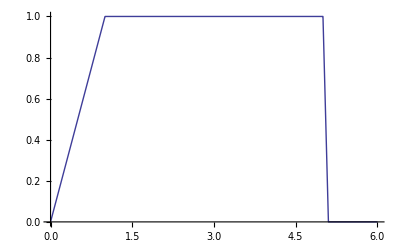

```mathematica
Plot[Which[t<1,t,1<t<5,1,5<t<5.1,1-10(t-5),t>5.1,0],{t,0,6}]
```

```mathematica
ListPlot[Transpose[{infos[[Position[infos,ToExpression[#]]⟦1,1⟧,1]]&/@nums,GetShift/@res}]]
```

```mathematica
Export["shifts.dat",Prepend[SortBy[Flatten/@Transpose[{{infos[[Position[infos,ToExpression[#]]⟦1,1⟧]],ToExpression[cs[[Position[cs,ToString[#]]⟦1,1⟧,1]]]}&/@nums,CutNumber[GetShift[#],5]&/@res}],1000#⟦4⟧+#⟦1⟧&],{"Time point","Iter","Rey","rc","Shift"}],"Table"]
```

```mathematica
Export["shifts.dat",Prepend[Sort[MapThread[{CutNumber[#1⟦1⟧,4],StringJoin@PadLeft[Characters[ToString@#1⟦2⟧],8," "],Round[#1⟦3⟧],0.45,CutNumber[#2,5]}&,{infos,GetShift/@res}]],{"Time","Iteration","Rey","rc","Shift"}],"Table"]
```

shifts.dat

```mathematica
ListLimit[Take[Transpose[{First/@SortBy[Most/@infos,Last],GetShift/@res}],{150,270}],CutValues->False,Shift->False,ApproximationReport->{LimitPlot,PolynomDegree}]
```

```mathematica
Clear[GetInflectionPoint];
GetInflectionPoint[snap_,κ_,add_String:"",viv_:True]:=Block[{nx,points},
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_16_"<>ToString[snap]<>".snp",5,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{If[κ==0,0,1/κ],0},ProcDistrib->{4,4},NumberOfRefs->2];
nx=Length[coor[[1]]]-2ghost;
If[viv,Print@ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine,FrameLabel->"κ="<>ToString[κ]<>add,DataRange->{First@bounds,{-1,1}}];
Print[ListPlot[vx[[All,nx/2+ghost]],DataRange->{-1,1}]]];
points=Extract[(coor[[1]]-Mean@bounds[[1]])[[ghost+1;;-1-ghost]],{Pick[Range[nx-1],(Times@@#<0)&/@Partition[vx[[ghost+1;;-1-ghost,nx/2+ghost]],2,1]]}ᵀ];
If[Length[points]>1,Print["Обнаружено более одной точки смены направления течения: ",points]];
If[Length[points]<1,Print["Нет смены направления"];If[vx[[nx/2+ghost,nx/2+ghost]]>0,1,-1],Last[points]]
]
GetInflectionPointNew[κ_,R_,F_,viv_:True]:=Block[{nx,points},
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow(kappa="<>ToString@κ<>",Re="<>ToString@R<>",F="<>ToString@F<>").snp",5,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{If[ToExpression@κ==0,0,1/ToExpression@κ],0},ProcDistrib->{4,4},NumberOfRefs->2];
nx=Length[coor[[1]]]-2ghost;
If[viv,Print@ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine,FrameLabel->"κ="<>ToString[κ]<>",Re="<>ToString@R<>",F="<>ToString@F,DataRange->{First@bounds,{-1,1}}];
Print[ListPlot[vx[[All,nx/2+ghost]],DataRange->{-1,1}]]];
points=Extract[(coor[[1]]-Mean@bounds[[1]])[[ghost+1;;-1-ghost]],{Pick[Range[nx-1],(Times@@#<0)&/@Partition[vx[[ghost+1;;-1-ghost,nx/2+ghost]],2,1]]}ᵀ];
If[Length[points]>1,Print["Обнаружено более одной точки смены направления течения: ",points]];
If[Length[points]<1,Print["Нет смены направления"];If[vx[[nx/2+ghost,nx/2+ghost]]>0,1,-1],Last[points]]
]
```

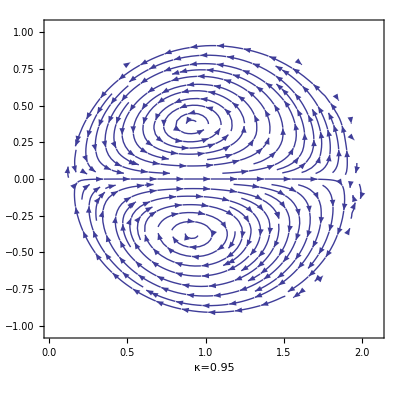

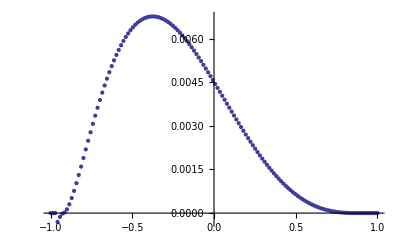

0.929688

```mathematica
GetInflectionPoint[157889,0.95]
```

```mathematica
0.72 √0.95
```

0.701769

```mathematica
pars=Union[fins[[All,1;;2]]];
Manipulate[ListLinePlot[Map[ToExpression,Union[{#[[1,3]],#[[2]]}&/@Select[{fins,res}ᵀ,#[[1,1;;2]]==pars[[i]]&]],{2}],AxesLabel->{"F","x_infl"},PlotRange->{Automatic,{-1,1}},PlotLabel->"κ="<>ToString[pars⟦i,1⟧]<>"; Re="<>ToString[pars⟦i,2⟧]],{i,1,Length[pars],1}]
```

Transpose::nmtx: The first two levels of {fins,{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«474»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«474»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«474»},«46»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«474»},«474»},«3»,{{0.00022222,«49»,«474»},«49»,«474»}}} cannot be transposed.

Part::take: Cannot take positions 1 through 2 in fins.

Part::partd: Part specification pars⟦3⟧ is longer than depth of object.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partd: Part specification pars⟦3,1⟧ is longer than depth of object.

Part::partd: Part specification pars⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Reverse/@Select[Map[ToExpression,Union[{#[[1,3]],#[[2]]}&/@Select[{fins,res}ᵀ,#[[1,1;;2]]==pars[[6]]&]],{2}],Abs[#[[2]]]≠1.&]
```

{{0.929688,-0.3},{0.617188,-0.4},{0.351563,-0.5},{0.117188,-0.6},{-0.0703125,-0.7}}

```mathematica
Append[ToExpression/@pars[[6]],Interpolation[%][0.]]
```

{0.95,7.,-0.659774}

```mathematica
vort4={{0.5,1.,-0.15,-0.3400427495193755,-0.5},{0.5,10.,-0.2,-0.3366685922981269,-0.45},{0.95,0.72,-0.3,-0.6601287366912366,-1.4},{0.95,7.,-0.3,-0.659774328765597,-1}};
```

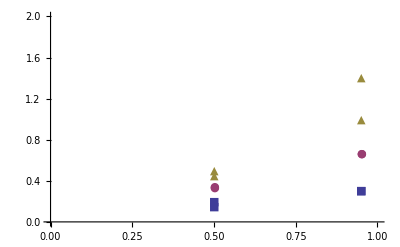

```mathematica
ListPlot[{{#[[1]],-#[[3]]}&/@vort4,{#[[1]],-#[[4]]}&/@vort4,{#[[1]],-#[[5]]}&/@vort4},PlotMarkers->{■,●,▲},PlotRange->{{0,1},{0,2}}]
```

```mathematica
vort2={ToExpression@#[[1,1]],-ToExpression@#[[1,3]]}&/@Select[{fins,res}ᵀ,Last[#]>0.95&];
vort4={ToExpression@#[[1,1]],-ToExpression@#[[1,3]]}&/@Select[{fins,res}ᵀ,-0.95≤Last[#]≤0.95&];
vorti2={ToExpression@#[[1,1]],-ToExpression@#[[1,3]]}&/@Select[{fins,res}ᵀ,Last[#]<-0.95&];
```

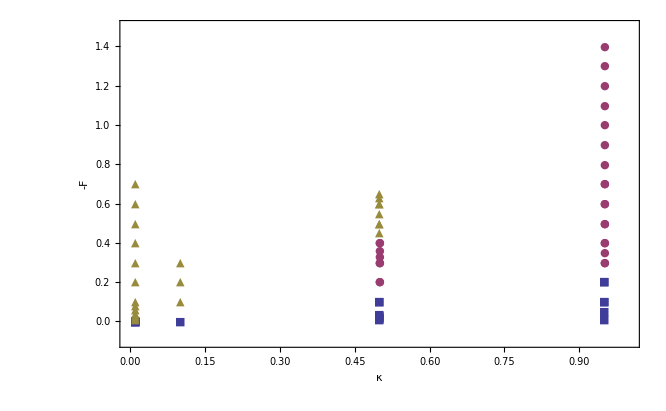

```mathematica
ListPlot[{vort2,vort4,vorti2},PlotMarkers->{■,●,▲},PlotRange->{{0,1},{-0.1,1.5}},Axes->False,Frame->True,FrameLabel->{"κ","-F"}]
```

```mathematica
Export["rotation-map.eps",%,ImageResolution->80,ImageSize->300];
```

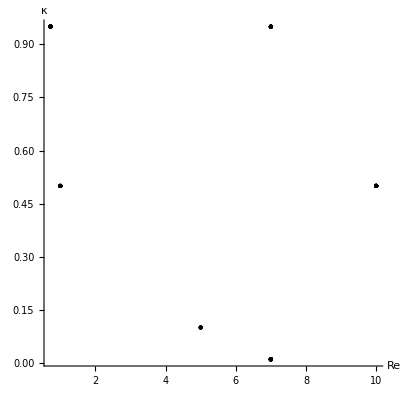

```mathematica
Graphics[Point[{ToExpression@#[[1,2]],ToExpression@#[[1,1]]}]&/@({fins,res}ᵀ),Axes->True,AspectRatio->1,AxesOrigin->{0,0},AxesLabel->{"Re","κ"}]
```

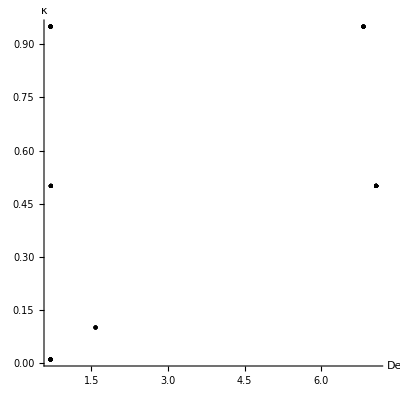

```mathematica
Graphics[Point[{ToExpression@#[[1,2]] √(ToExpression@#[[1,1]]),ToExpression@#[[1,1]]}]&/@({fins,res}ᵀ),Axes->True,AspectRatio->1,AxesOrigin->{0,0},AxesLabel->{"De","κ"}]
```

```mathematica
{#[[1,1]],#[[1,2]],#[[1,3]],#[[2]]}&/@({fins,res}ᵀ)
```

{{0.01,7.00,-0.0001,1},{0.01,7.00,-0.001,1},{0.01,7.00,-0.004,1},{0.01,7.00,-0.00,1},{0.01,7.00,-0.01,-1},{0.01,7.00,-0.02,-1},{0.01,7.00,-0.03,-1},{0.01,7.00,-0.04,-1},{0.01,7.00,-0.06,-1},{0.01,7.00,-0.08,-1},{0.01,7.00,-0.10,-1},{0.01,7.00,-0.20,-1},{0.01,7.00,-0.30,-1},{0.01,7.00,-0.40,-1},{0.01,7.00,-0.50,-1},{0.01,7.00,-0.60,-1},{0.01,7.00,-0.70,-1},{0.10,5.00,-0.00,1},{0.10,5.00,-0.10,-1},{0.10,5.00,-0.20,-1},{0.10,5.00,-0.30,-1},{0.50,10.00,-0.015,1},{0.50,10.00,-0.01,1},{0.50,10.00,-0.025,1},{0.50,10.00,-0.02,1},{0.50,10.00,-0.035,1},{0.50,10.00,-0.03,1},{0.50,10.00,-0.10,1},{0.50,10.00,-0.20,0.914063},{0.50,10.00,-0.30,0.273438},{0.50,10.00,-0.40,-0.554688},{0.50,10.00,-0.45,-1},{0.50,10.00,-0.50,-1},{0.50,10.00,-0.55,-1},{0.50,10.00,-0.60,-1},{0.50,10.00,-0.65,-1},{0.50,1.00,-0.10,1},{0.50,1.00,-0.20,0.914063},{0.50,1.00,-0.30,0.273438},{0.50,1.00,-0.33,0.0703125},{0.50,1.00,-0.36,-0.148438},{0.50,1.00,-0.40,-0.570313},{0.50,1.00,-0.50,-1},{0.50,1.00,-0.60,-1},{0.50,1.00,-0.63,-1},{0.95,0.72,-0.10,1},{0.95,0.72,-0.20,1},{0.95,0.72,-0.30,0.929688},{0.95,0.72,-0.35,0.773438},{0.95,0.72,-0.40,0.617188},{0.95,0.72,-0.50,0.351563},{0.95,0.72,-0.60,0.117188},{0.95,0.72,-0.70,-0.0703125},{0.95,0.72,-0.80,-0.226563},{0.95,0.72,-0.90,-0.367188},{0.95,0.72,-1.00,-0.492188},{0.95,0.72,-1.10,-0.601563},{0.95,0.72,-1.20,-0.695313},{0.95,0.72,-1.30,-0.773438},{0.95,0.72,-1.40,-0.851563},{0.95,7.00,-0.01,1},{0.95,7.00,-0.05,1},{0.95,7.00,-0.10,1},{0.95,7.00,-0.20,1},{0.95,7.00,-0.30,0.929688},{0.95,7.00,-0.40,0.617188},{0.95,7.00,-0.50,0.351563},{0.95,7.00,-0.60,0.117188},{0.95,7.00,-0.70,-0.0703125}}

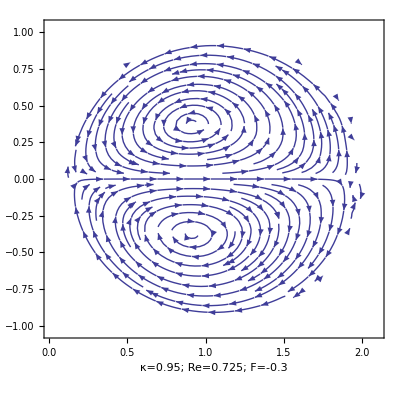

-Graphics-

```mathematica
CellPrint[Cell["Проверка на 4-вихревое течение","Section"]];
res=(CellPrint[Cell["κ="<>ToString@#[[1]]<>"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]]<>"; snap="<>ToString@#[[4]],"Subsection"]];
GetInflectionPoint[#[[4]],#[[1]],"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]]])&/@fins
```

```mathematica
{fins0,res0}={fins,res};
```

```mathematica
fins=
First/@StringCases[FileNames["pumpflow(*).snp"],"pumpflow(kappa="~~k__~~",Re="~~r__~~",F="~~f__~~").snp":>{k,r,f}]
```

{{0.01,7.00,-0.00},{0.01,7.00,-0.01},{0.01,7.00,-0.02},{0.01,7.00,-0.03},{0.01,7.00,-0.04},{0.01,7.00,-0.06},{0.01,7.00,-0.08},{0.01,7.00,-0.10},{0.01,7.00,-0.20},{0.01,7.00,-0.30},{0.01,7.00,-0.40},{0.01,7.00,-0.50},{0.01,7.00,-0.60},{0.01,7.00,-0.70},{0.10,5.00,-0.00},{0.10,5.00,-0.10},{0.10,5.00,-0.20},{0.10,5.00,-0.30},{0.50,10.00,-0.015},{0.50,10.00,-0.01},{0.50,10.00,-0.025},{0.50,10.00,-0.02},{0.50,10.00,-0.035},{0.50,10.00,-0.03},{0.50,10.00,-0.10},{0.50,10.00,-0.20},{0.50,10.00,-0.30},{0.50,10.00,-0.40},{0.50,10.00,-0.45},{0.50,10.00,-0.50},{0.50,10.00,-0.55},{0.50,10.00,-0.60},{0.50,10.00,-0.65},{0.50,1.00,-0.10},{0.50,1.00,-0.20},{0.50,1.00,-0.30},{0.50,1.00,-0.33},{0.50,1.00,-0.36},{0.50,1.00,-0.40},{0.50,1.00,-0.50},{0.50,1.00,-0.60},{0.50,1.00,-0.63},{0.95,0.72,-0.10},{0.95,0.72,-0.20},{0.95,0.72,-0.30},{0.95,0.72,-0.35},{0.95,0.72,-0.40},{0.95,0.72,-0.50},{0.95,0.72,-0.60},{0.95,0.72,-0.70},{0.95,0.72,-0.80},{0.95,0.72,-0.90},{0.95,0.72,-1.00},{0.95,0.72,-1.10},{0.95,0.72,-1.20},{0.95,0.72,-1.30},{0.95,0.72,-1.40},{0.95,7.00,-0.01},{0.95,7.00,-0.05},{0.95,7.00,-0.10},{0.95,7.00,-0.20},{0.95,7.00,-0.30},{0.95,7.00,-0.40},{0.95,7.00,-0.50},{0.95,7.00,-0.60},{0.95,7.00,-0.70}}

```mathematica
fins=Drop[fins,{4}];
```

```mathematica
PrependTo[fins,{"0.01","7.00","-0.0001"}];
PrependTo[res,1];
```

```mathematica
GetInflectionPointNew["0.01","7.00","-0.004"]
```

```mathematica
CellPrint[Cell["Проверка на 4-вихревое течение","Section"]];
res=(CellPrint[Cell["κ="<>ToString@#[[1]]<>"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]],"Subsection"]];
GetInflectionPointNew@@#)&/@fins
```

## Проверка на 4-вихревое течение

### κ=0.01; Re=7.00; F=-0.00

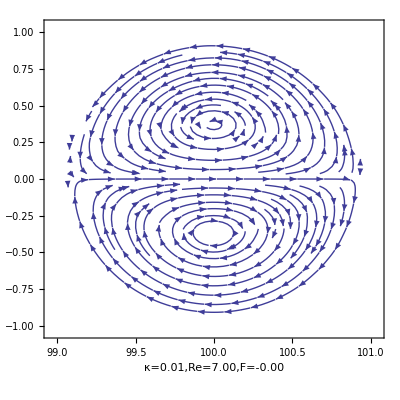

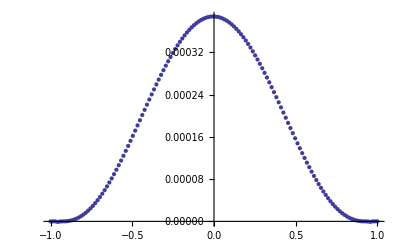

Нет смены направления

### κ=0.01; Re=7.00; F=-0.01

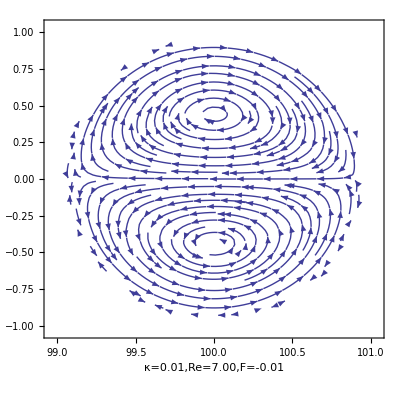

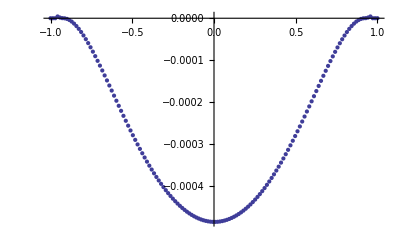

Нет смены направления

### κ=0.01; Re=7.00; F=-0.02

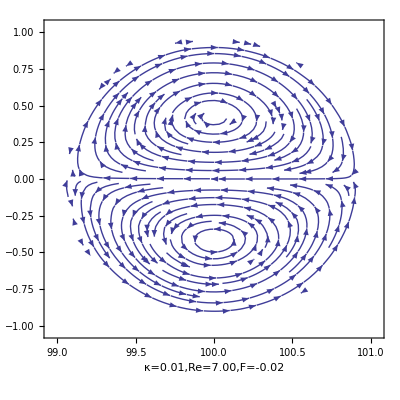

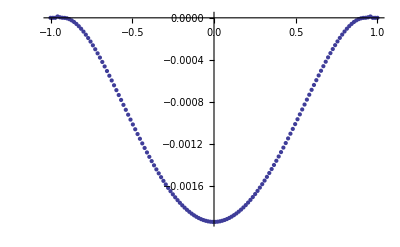

Нет смены направления

### κ=0.01; Re=7.00; F=-0.03

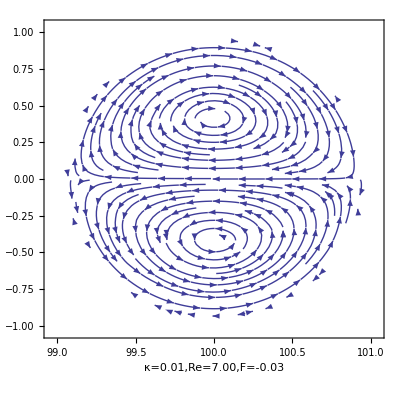

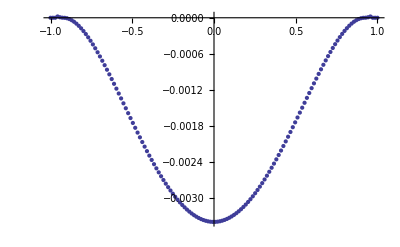

Нет смены направления

### κ=0.01; Re=7.00; F=-0.04

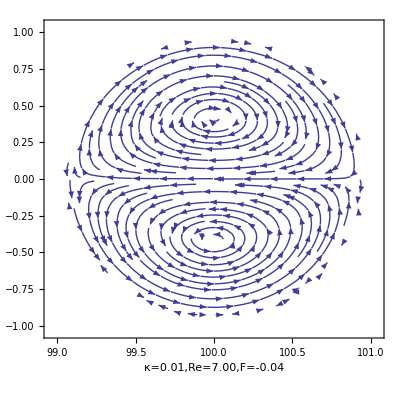

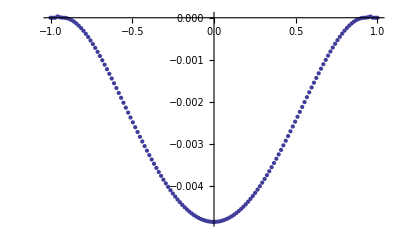

Нет смены направления

### κ=0.01; Re=7.00; F=-0.06

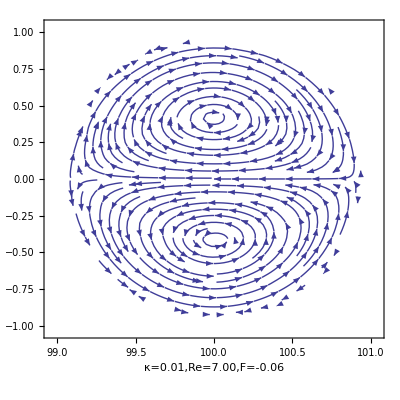

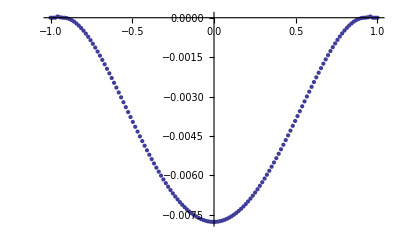

Нет смены направления

### κ=0.01; Re=7.00; F=-0.08

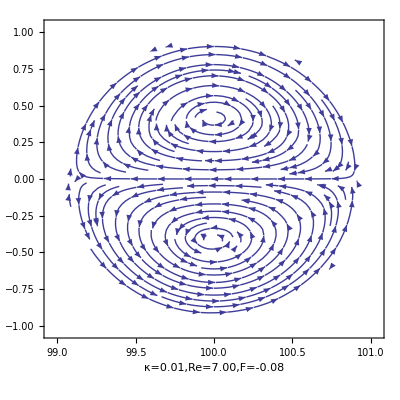

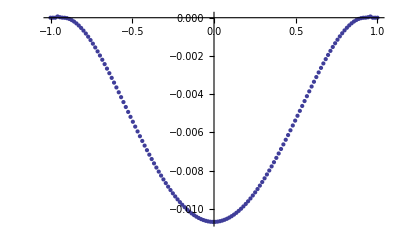

Нет смены направления

### κ=0.01; Re=7.00; F=-0.10

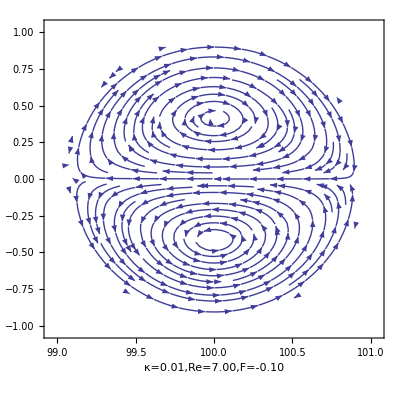

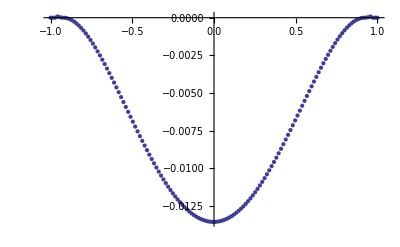

Нет смены направления

### κ=0.01; Re=7.00; F=-0.20

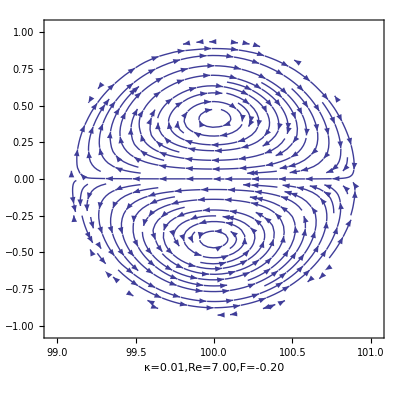

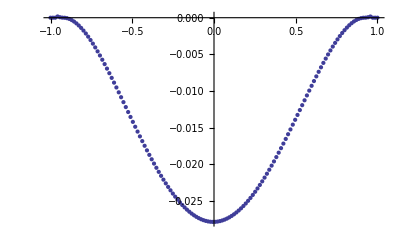

Нет смены направления

### κ=0.01; Re=7.00; F=-0.30

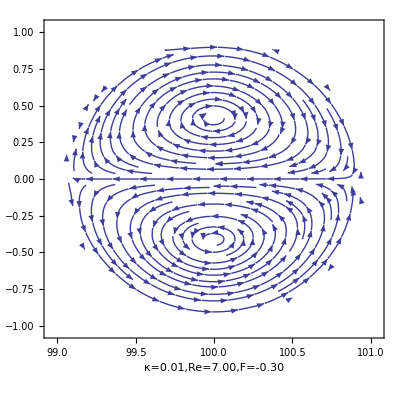

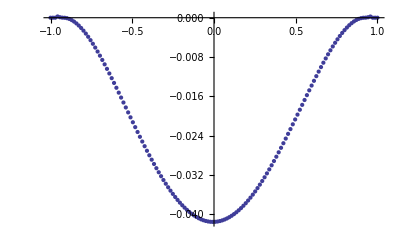

Нет смены направления

### κ=0.01; Re=7.00; F=-0.40

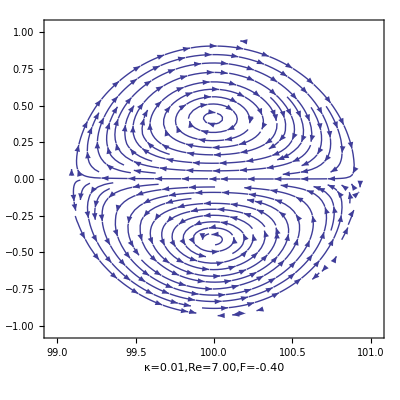

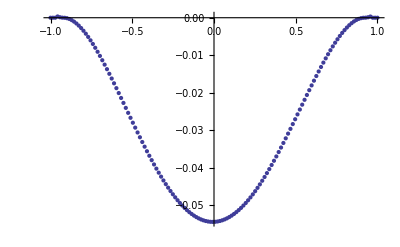

Нет смены направления

### κ=0.01; Re=7.00; F=-0.50

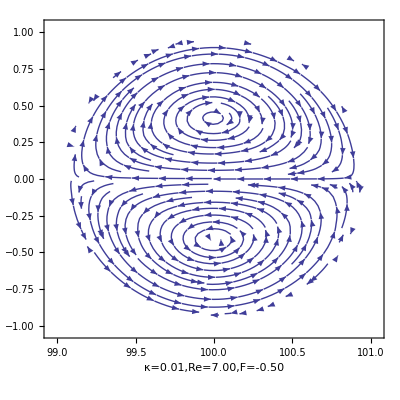

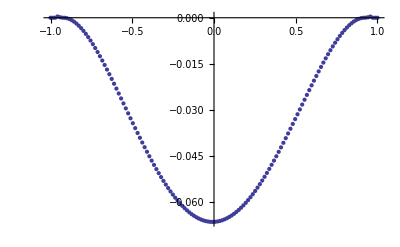

Нет смены направления

### κ=0.01; Re=7.00; F=-0.60

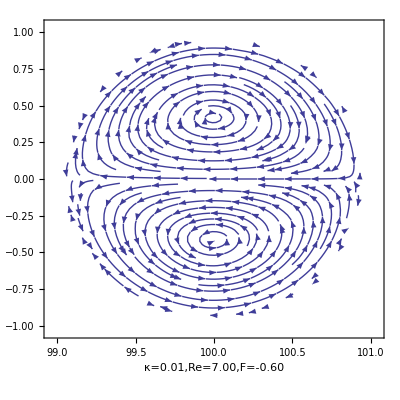

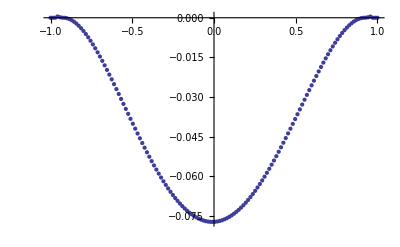

Нет смены направления

### κ=0.01; Re=7.00; F=-0.70

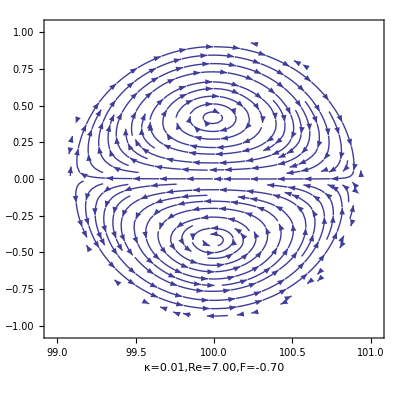

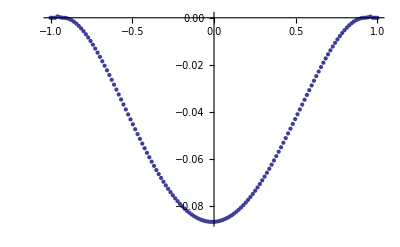

Нет смены направления

### κ=0.10; Re=5.00; F=-0.00

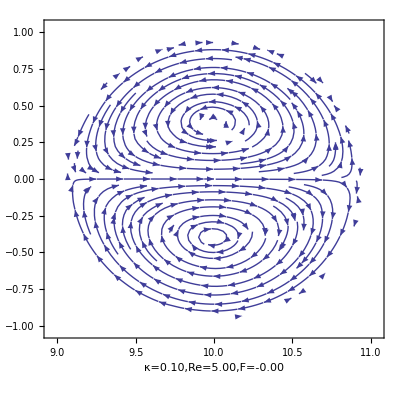

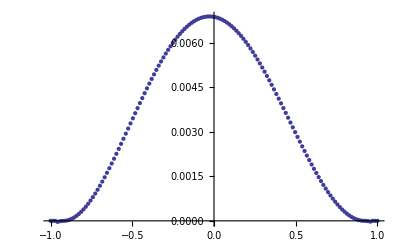

Нет смены направления

### κ=0.10; Re=5.00; F=-0.10

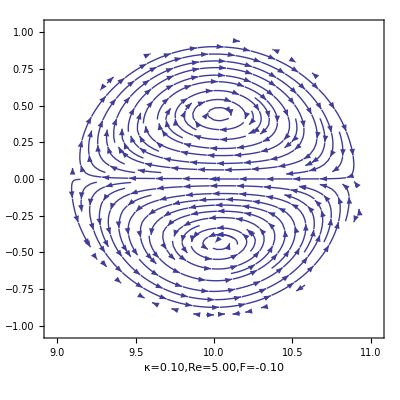

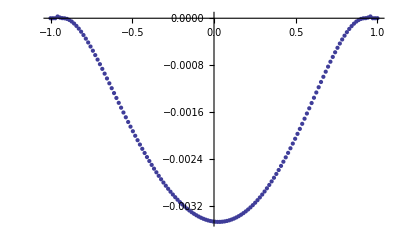

Нет смены направления

### κ=0.10; Re=5.00; F=-0.20

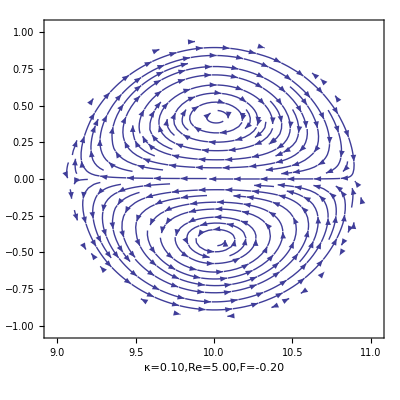

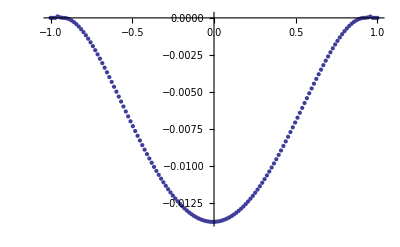

Нет смены направления

### κ=0.10; Re=5.00; F=-0.30

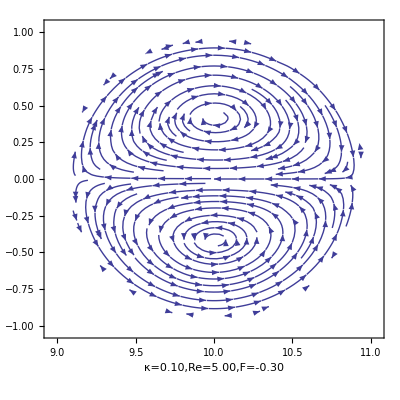

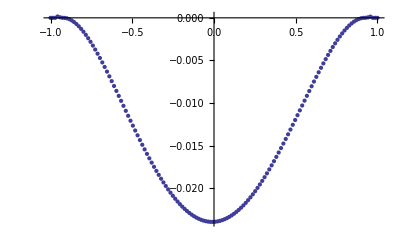

Нет смены направления

### κ=0.50; Re=10.00; F=-0.015

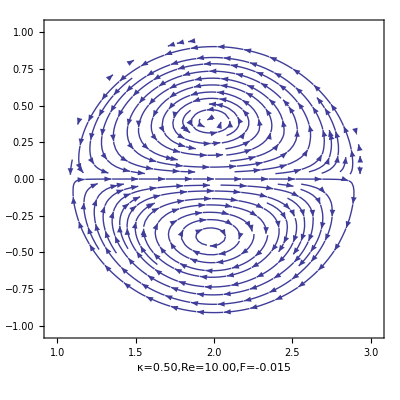

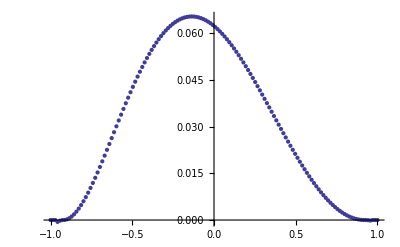

Нет смены направления

### κ=0.50; Re=10.00; F=-0.01

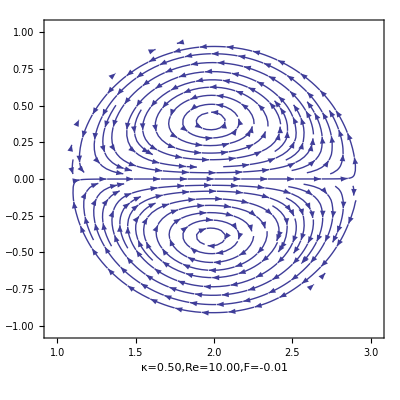

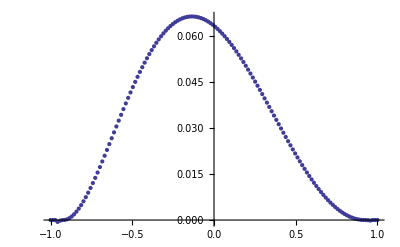

Нет смены направления

### κ=0.50; Re=10.00; F=-0.025

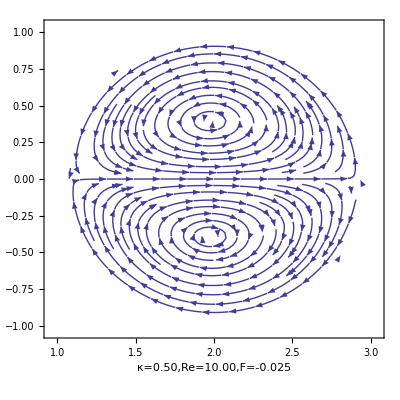

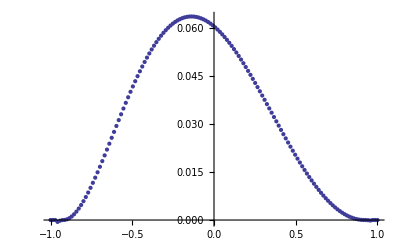

Нет смены направления

### κ=0.50; Re=10.00; F=-0.02

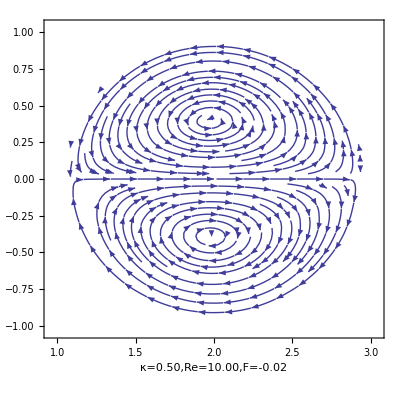

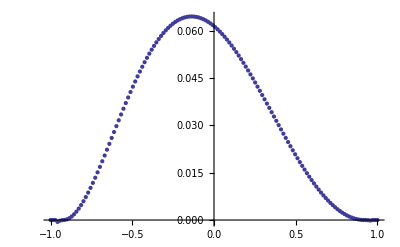

Нет смены направления

### κ=0.50; Re=10.00; F=-0.035

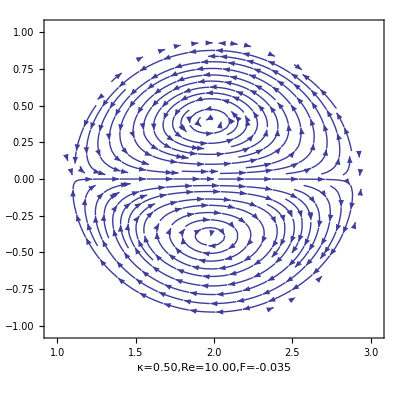

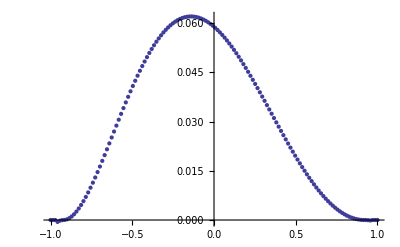

Нет смены направления

### κ=0.50; Re=10.00; F=-0.03

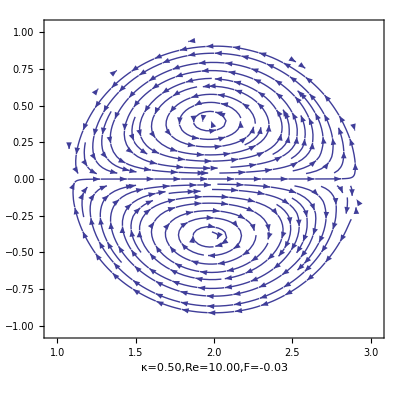

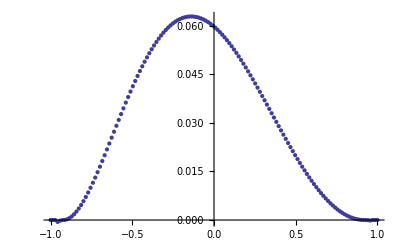

Нет смены направления

### κ=0.50; Re=10.00; F=-0.10

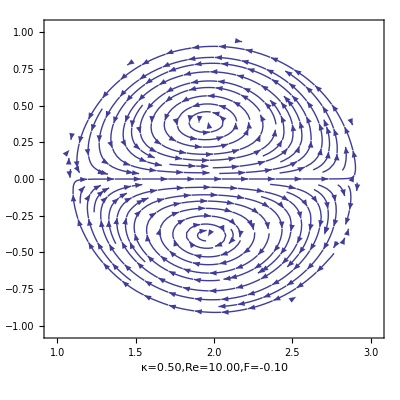

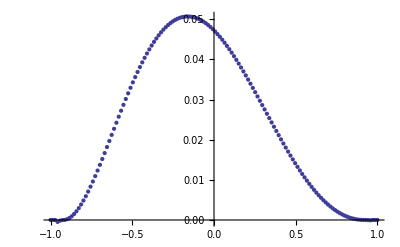

Нет смены направления

### κ=0.50; Re=10.00; F=-0.20

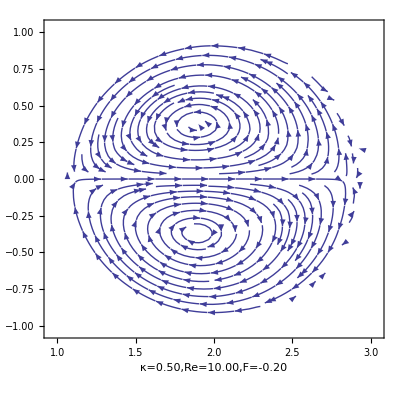

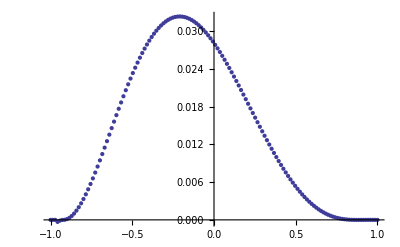

### κ=0.50; Re=10.00; F=-0.30

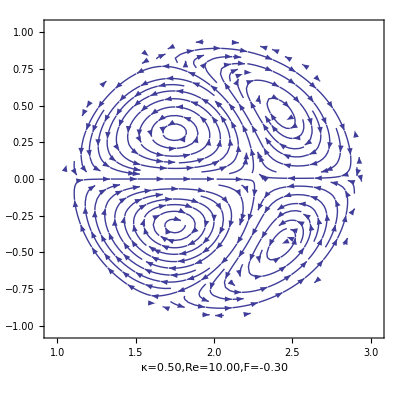

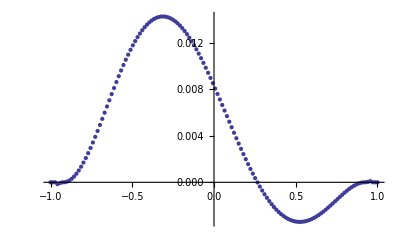

### κ=0.50; Re=10.00; F=-0.40

-Graphics-

-Graphics-

Обнаружено более одной точки смены направления течения: {-0.882813,-0.554688}

### κ=0.50; Re=10.00; F=-0.45

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=10.00; F=-0.50

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=10.00; F=-0.55

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=10.00; F=-0.60

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=10.00; F=-0.65

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=1.00; F=-0.10

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=1.00; F=-0.20

-Graphics-

-Graphics-

### κ=0.50; Re=1.00; F=-0.30

-Graphics-

-Graphics-

### κ=0.50; Re=1.00; F=-0.33

-Graphics-

-Graphics-

### κ=0.50; Re=1.00; F=-0.36

-Graphics-

-Graphics-

### κ=0.50; Re=1.00; F=-0.40

-Graphics-

-Graphics-

Обнаружено более одной точки смены направления течения: {-0.882813,-0.570313}

### κ=0.50; Re=1.00; F=-0.50

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=1.00; F=-0.60

-Graphics-

-Graphics-

Нет смены направления

### κ=0.50; Re=1.00; F=-0.63

-Graphics-

-Graphics-

Нет смены направления

### κ=0.95; Re=0.72; F=-0.10

-Graphics-

-Graphics-

Нет смены направления

### κ=0.95; Re=0.72; F=-0.20

-Graphics-

-Graphics-

Нет смены направления

### κ=0.95; Re=0.72; F=-0.30

-Graphics-

-Graphics-

### κ=0.95; Re=0.72; F=-0.35

-Graphics-

```mathematica
Export["rotat0.35.eps",-Graphics-,ImageResolution->80,ImageSize->600]
```

rotat0.35.eps

```mathematica
f
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.40

-Graphics-

```mathematica
Export["rotat0.40.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.50

-Graphics-

```mathematica
Export["rotat0.50.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.60

-Graphics-

```mathematica
Export["rotat0.60.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

```mathematica
k
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.70

-Graphics-

```mathematica
Export["rotat0.70.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.80

-Graphics-

```mathematica
Export["rotat0.80.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

-Graphics-

### κ=0.95; Re=0.72; F=-0.90

-Graphics-

```mathematica
Export["rotat0.90.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

-Graphics-

### κ=0.95; Re=0.72; F=-1.00

-Graphics-

```mathematica
Export["rotat1.00.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

```mathematica
ju
```

-Graphics-

### κ=0.95; Re=0.72; F=-1.10

-Graphics-

```mathematica
Export["rotat1.10.eps",-Graphics-,ImageResolution->80,ImageSize->600];
```

## Проверка типов ячеек

```mathematica
ghost=3;
```

```mathematica
{node,{rr,rz}}=ReadAuxFiles2D[{"node","ref"},NumberOfRefs->2,ProcDistrib->{2,2}];
```

```mathematica
Union[Flatten[node]]
```

{4,8,12,20}

```mathematica
ListDensityPlot[node]
```

```mathematica
ListDensityPlot[Transpose[BitAnd[node,8]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
DisplayTogether[ListDensityPlot[node],gc];
```

```mathematica
ListDensityPlot/@{node,rr,rz};
```

```mathematica
ListContourPlot[node]
ListContourPlot[rr]
ListContourPlot[rz]
```